```mathematica
Import["https://projecteuler.net/problem=18","HTML"]
```

About   Archives   Recent   News   Register   Sign In    
 
 
     
 
   Maximum path sum I
 Published on Friday, 31st May 2002, 06:00 pm; Solved by 138262;
Difficulty rating: 5%
Problem 18  
 
By starting at the top of the triangle below and moving to adjacent numbers on the row below, the maximum total from top to bottom is 23.  
3
7 4
 2 4 6
 8 5 9 3  
That is, 3 + 7 + 4 + 9 = 23.  
Find the maximum total from top to bottom of the triangle below:  
75
 95 64
 17 47 82
 18 35 87 10
 20 04 82 47 65
 19 01 23 75 03 34
 88 02 77 73 07 63 67
 99 65 04 28 06 16 70 92
 41 41 26 56 83 40 80 70 33
 41 48 72 33 47 32 37 16 94 29
 53 71 44 65 25 43 91 52 97 51 14
 70 11 33 28 77 73 17 78 39 68 17 57
 91 71 52 38 17 14 91 43 58 50 27 29 48
 63 66 04 68 89 53 67 30 73 16 69 87 40 31
 04 62 98 27 23 09 70 98 73 93 38 53 60 04 23  
NOTE: As there are only 16384 routes, it is possible to solve this problem by trying every route. However, Problem 67 , is the same challenge with a triangle containing one-hundred rows; it cannot be solved by brute force, and requires a clever method! ;o)  
 
   
 Project Euler: Copyright Information | Privacy Policy

```mathematica
Import["https://projecteuler.net/problem=18","Data"]
```

Import::fmterr: Cannot import data as RDFXML format.

$Failed

```mathematica
{{75} {95,64},{17,47,82},{18,35,87,10},{20,04,82,47,65},{19,01,23,75,03,34},{88,02,77,73,07,63,67},{99,65,04,28,06,16,70,92},{41,41,26,56,83,40,80,70,33},{41,48,72,33,47,32,37,16,94,29},{53,71,44,65,25,43,91,52,97,51,14},{70,11,33,28,77,73,17,78,39,68,17,57},{91,71,52,38,17,14,91,43,58,50,27,29,48},{63,66,04,68,89,53,67,30,73,16,69,87,40,31},{04,62,98,27,23,09,70,98,73,93,38,53,60,04,23}}
```

Thread::tdlen: Objects of unequal length in {75} {95,64} cannot be combined.

{{75} {95,64},{17,47,82},{18,35,87,10},{20,4,82,47,65},{19,1,23,75,3,34},{88,2,77,73,7,63,67},{99,65,4,28,6,16,70,92},{41,41,26,56,83,40,80,70,33},{41,48,72,33,47,32,37,16,94,29},{53,71,44,65,25,43,91,52,97,51,14},{70,11,33,28,77,73,17,78,39,68,17,57},{91,71,52,38,17,14,91,43,58,50,27,29,48},{63,66,4,68,89,53,67,30,73,16,69,87,40,31},{4,62,98,27,23,9,70,98,73,93,38,53,60,4,23}}

```mathematica
Nest[f,x,n]
```

Nest::intnm: Non-negative machine-sized integer expected at position 3 in Nest[f,x,n].

Nest[f,x,n]

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

```mathematica
n[f,x,n]
```

n[f,x,n]

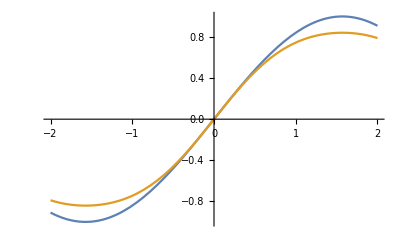

```mathematica
Plot[{Sin[x],Sin[Sin[x]]},{x,-2,2}]
```

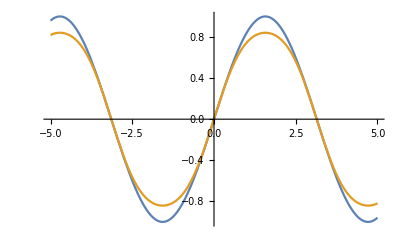

```mathematica
Plot[{Sin[x],Sin[Sin[x]]},{x,-5,5}]
```

```mathematica
Solve[α Sin[x]==Sin[Sin[x]],α]
```

{{α→Csc[x] Sin[Sin[x]]}}

```mathematica
FindInstance[α Sin[x]==Sin[Sin[x]],α]
```

FindInstance::exvar: The system contains a nonconstant expression Sin[x] independent of variables {α}.

FindInstance[α Sin[x]==Sin[Sin[x]],α]

```mathematica
Sin[π/2]
```

1

```mathematica
Sin[Sin[π/2]]
```

Sin[1]

```mathematica
N[Sin[1]]
```

0.841471

```mathematica
Solve[Sin[1]==a π,a]
```

{{a→Sin[1]/π}}

```mathematica
Nest[Sin,x,10]
```

Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[x]]]]]]]]]]

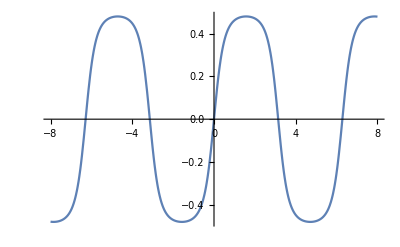

```mathematica
Plot[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[Sin[x]]]]]]]]]],{x,-8,8}]
```

```mathematica
Manipulate[
Plot[{Sin[x],Nest[Sin,x,n]},{x,-10,10}]
,{n,1,10,1}]
```

```mathematica
Manipulate[
Plot[{Sin[x],Nest[Sin,x,n]},{x,-10,10}]
,{n,1,100,10}]
```

```mathematica
FullSimplify[ArcCurvature[{x,Nest[Sin,x,100]},x],x∈Reals]
```

$Aborted

```mathematica
FullSimplify[ArcCurvature[{x,Nest[Sin,x,10]},x],x∈Reals]
```

$Aborted

```mathematica
FullSimplify[ArcCurvature[{x,Nest[Sin,x,2]},x],x∈Reals]
```

Abs[Cos[Sin[x]] Sin[x]+Cos[x]^2 Sin[Sin[x]]]/((1+Cos[x]^2 Cos[Sin[x]]^2)^(3/2))

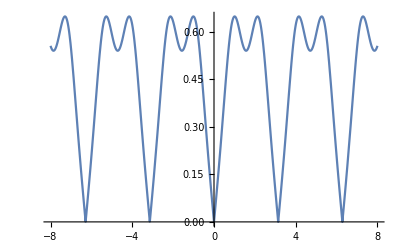

```mathematica
Plot[Abs[Cos[Sin[x]] Sin[x]+Cos[x]^2 Sin[Sin[x]]]/((1+Cos[x]^2 Cos[Sin[x]]^2)^(3/2)),{x,-8,8}]
```

```mathematica
FullSimplify[ArcCurvature[{x,Sin[x]},x],x∈Reals]
```

Abs[Sin[x]]/((1+Cos[x]^2)^(3/2))

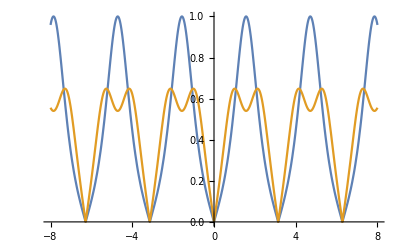

```mathematica
Plot[{Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),Abs[Cos[Sin[x]] Sin[x]+Cos[x]^2 Sin[Sin[x]]]/((1+Cos[x]^2 Cos[Sin[x]]^2)^(3/2))},{x,-8,8}]
```

```mathematica
FullSimplify[ArcCurvature[{x,Nest[Sin,x,3]},x],x∈Reals]
```

$Aborted

```mathematica
Plot[{Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),Abs[Cos[Sin[x]] Sin[x]+Cos[x]^2 Sin[Sin[x]]]/((1+Cos[x]^2 Cos[Sin[x]]^2)^(3/2))},{x,-8,8}]
```

```mathematica
FullSimplify[ArcCurvature[{x,f[x]},x],x∈Reals]
```

√(f''[x]^2/((1+f'[x]^2)^3))

```mathematica
FullSimplify[ArcCurvature[{x,f[f[x]]},x],x∈Reals]
```

√(((f'[f[x]] f''[x]+f'[x]^2 f''[f[x]])^2)/((1+f'[x]^2 f'[f[x]]^2)^3))

```mathematica
FullSimplify[ArcCurvature[{x,f[f[f[x]]]},x],x∈Reals]
```

√(((f'[f[f[x]]] (f'[f[x]] f''[x]+f'[x]^2 f''[f[x]])+f'[x]^2 f'[f[x]]^2 f''[f[f[x]]])^2)/((1+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2)^3))

```mathematica
With[{f=Sin},
√(((f'[f[f[x]]] (f'[f[x]] f''[x]+f'[x]^2 f''[f[x]])+f'[x]^2 f'[f[x]]^2 f''[f[f[x]]])^2)/((1+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2)^3))
]
```

√(((Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])^2)/((1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2)^3))

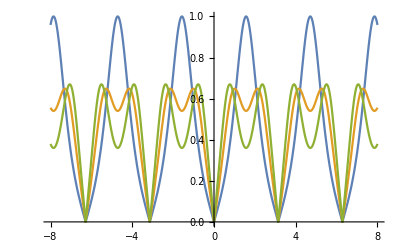

```mathematica
Plot[{Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),Abs[Cos[Sin[x]] Sin[x]+Cos[x]^2 Sin[Sin[x]]]/((1+Cos[x]^2 Cos[Sin[x]]^2)^(3/2)),√(((Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])^2)/((1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2)^3))},{x,-8,8}]
```

```mathematica
FullSimplify[ArcCurvature[{x,f[f[f[f[x]]]]},x],x∈Reals]
```

√(((f'[f[f[f[x]]]] (f'[f[f[x]]] (f'[f[x]] f''[x]+f'[x]^2 f''[f[x]])+f'[x]^2 f'[f[x]]^2 f''[f[f[x]]])+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2 f''[f[f[f[x]]]])^2)/((1+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2 f'[f[f[f[x]]]]^2)^3))

```mathematica
With[{f=Sin},
√(((f'[f[f[f[x]]]] (f'[f[f[x]]] (f'[f[x]] f''[x]+f'[x]^2 f''[f[x]])+f'[x]^2 f'[f[x]]^2 f''[f[f[x]]])+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2 f''[f[f[f[x]]]])^2)/((1+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2 f'[f[f[f[x]]]]^2)^3))
]
```

√((Cos[Sin[Sin[Sin[x]]]] (Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])-Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Sin[Sin[Sin[Sin[x]]]])^2/(1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Cos[Sin[Sin[Sin[x]]]]^2)^3)

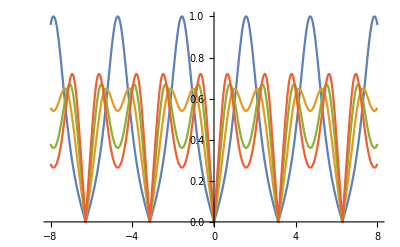

```mathematica
Plot[{Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),Abs[Cos[Sin[x]] Sin[x]+Cos[x]^2 Sin[Sin[x]]]/((1+Cos[x]^2 Cos[Sin[x]]^2)^(3/2)),√(((Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])^2)/((1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2)^3)),√((Cos[Sin[Sin[Sin[x]]]] (Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])-Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Sin[Sin[Sin[Sin[x]]]])^2/(1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Cos[Sin[Sin[Sin[x]]]]^2)^3)},{x,-8,8}]
```

```mathematica
FullSimplify[ArcCurvature[{x,f[f[f[f[f[x]]]]]},x],x∈Reals]
```

√((f'[f[f[f[f[x]]]]] (f'[f[f[f[x]]]] (f'[f[f[x]]] (f'[f[x]] f''[x]+f'[x]^2 f''[f[x]])+f'[x]^2 f'[f[x]]^2 f''[f[f[x]]])+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2 f''[f[f[f[x]]]])+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2 f'[f[f[f[x]]]]^2 f''[f[f[f[f[x]]]]])^2/(1+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2 f'[f[f[f[x]]]]^2 f'[f[f[f[f[x]]]]]^2)^3)

```mathematica
Plot[{Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),Abs[Cos[Sin[x]] Sin[x]+Cos[x]^2 Sin[Sin[x]]]/((1+Cos[x]^2 Cos[Sin[x]]^2)^(3/2)),√(((Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])^2)/((1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2)^3)),√((Cos[Sin[Sin[Sin[x]]]] (Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])-Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Sin[Sin[Sin[Sin[x]]]])^2/(1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Cos[Sin[Sin[Sin[x]]]]^2)^3)},{x,-8,8}]
```

```mathematica
With[{f=Sin},
√((f'[f[f[f[f[x]]]]] (f'[f[f[f[x]]]] (f'[f[f[x]]] (f'[f[x]] f''[x]+f'[x]^2 f''[f[x]])+f'[x]^2 f'[f[x]]^2 f''[f[f[x]]])+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2 f''[f[f[f[x]]]])+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2 f'[f[f[f[x]]]]^2 f''[f[f[f[f[x]]]]])^2/(1+f'[x]^2 f'[f[x]]^2 f'[f[f[x]]]^2 f'[f[f[f[x]]]]^2 f'[f[f[f[f[x]]]]]^2)^3)
]
```

√((Cos[Sin[Sin[Sin[Sin[x]]]]] (Cos[Sin[Sin[Sin[x]]]] (Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])-Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Sin[Sin[Sin[Sin[x]]]])-Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Cos[Sin[Sin[Sin[x]]]]^2 Sin[Sin[Sin[Sin[Sin[x]]]]])^2/(1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Cos[Sin[Sin[Sin[x]]]]^2 Cos[Sin[Sin[Sin[Sin[x]]]]]^2)^3)

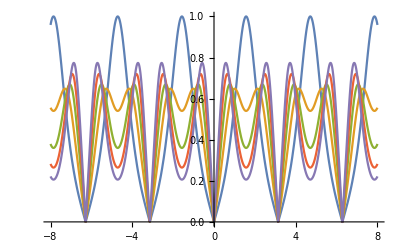

```mathematica
Plot[{Abs[Sin[x]]/((1+Cos[x]^2)^(3/2)),Abs[Cos[Sin[x]] Sin[x]+Cos[x]^2 Sin[Sin[x]]]/((1+Cos[x]^2 Cos[Sin[x]]^2)^(3/2)),√(((Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])^2)/((1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2)^3)),√((Cos[Sin[Sin[Sin[x]]]] (Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])-Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Sin[Sin[Sin[Sin[x]]]])^2/(1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Cos[Sin[Sin[Sin[x]]]]^2)^3),√((Cos[Sin[Sin[Sin[Sin[x]]]]] (Cos[Sin[Sin[Sin[x]]]] (Cos[Sin[Sin[x]]] (-Cos[Sin[x]] Sin[x]-Cos[x]^2 Sin[Sin[x]])-Cos[x]^2 Cos[Sin[x]]^2 Sin[Sin[Sin[x]]])-Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Sin[Sin[Sin[Sin[x]]]])-Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Cos[Sin[Sin[Sin[x]]]]^2 Sin[Sin[Sin[Sin[Sin[x]]]]])^2/(1+Cos[x]^2 Cos[Sin[x]]^2 Cos[Sin[Sin[x]]]^2 Cos[Sin[Sin[Sin[x]]]]^2 Cos[Sin[Sin[Sin[Sin[x]]]]]^2)^3)},{x,-8,8}]
```